# Analysis of the traction isolines for a single timeframe

## Figures and gifs for summer 23

by Joan Térmens

## Table of contents

Notebook setup

Folder configuration

Custom read of .txt and .msh files

Functions for FEM load and process

Visualization configuration

Demo analysis

Load the simulations

Load the parameters

Load the timeseries (integrated variables)

Load the local fields

Plot timeseries: CM velocity

Plot local fields

Static plots of timeframes

Dynamic plots

Export the visualizations as .gif

In development

Compute and visualize the curvature

Compute and visualize the phase field

## Notebook Setup

### Folder configuration

```mathematica
ClearAll;

SetDirectory[ParentDirectory[NotebookDirectory[]]]; (*Set the parent of the notebook's directory as the current working directory*)

simulNames={
"time_evol_1pi6_Lc50_08Rc",(*Simulation with custom paramters, Subscript[θ, c] = π/6 and Subscript[R, 0] = .8 Subscript[R, c]*)
"time_evol_1pi6_Lc50_Rc" (*Simulation with custom paramters, Subscript[θ, c] = π/6 and Subscript[R, 0] = Subscript[R, c]*)
};

(*Simulations's description*)
simulLegend=<|
"time_evol_1pi6_Lc50_08Rc"->"θ_c = π/6, R_0 = .8R_c",
"time_evol_1pi6_Lc50_Rc"->"θ_c = π/6, R_0 = R_c"
|>;

(*Folder management*)
pathFolder=FileNameJoin[{"Simul_runs","optimized_params_time_evol"}]; (*All the simulations to load are stored in the same folder*)

(*For simulations scattered across multiple folders use a template as the one below
pathFolder[simulName_]:= Which[
MemberQ[simuls1,simulName],".../simuls1_folder",
MemberQ[simuls2,simulName],".../simuls2_folder",
MemberQ[simul3,simulName],".../simuls3_folder"
];
pathSimul[simulName_] := pathFolder[simulName]<>simulName;
*)
pathSimul[simulName_]:=FileNameJoin[{pathFolder,simulName}];
pathMeshes[simulName_]:=FileNameJoin[{pathFolder,simulName,"msh"}];
pathSolutions[simulName_]:=FileNameJoin[{pathFolder,simulName,"local_sol"}];
pathResults = FileNameJoin[{NotebookDirectory[],"results"}];
```

### Custom read of .txt and .msh files

```mathematica
(*Custom read of a file, skips the headers (first nheader lines) and reads everything else as numbers, while converting lines into lists*)
ReadFile[filename_,nheader_:0]:=Module[{strm,data},
strm=OpenRead[filename];
(*Skip Header*)
Skip[strm,String,nheader];
data=ReadList[strm,Number,RecordLists->True]; (*read all the numbers on each line of the file into a separate list*)
Close[strm];
data
]

(*Custom read of an .msh file. Colud save the mesh labels and returns nV (num. vertices), nT (num.triangles), nbE (num. boundary edges), together with lists of the vertices, triangles and boundary edges.*)
ReadMshFile[filename_,saveLabels_:False]:=Module[{strm,data,nV,nT,nbE,iniIndex,lastCol,meshVertices,meshTriangles,bmeshEdges},
strm=OpenRead[filename];
data=ReadList[strm,Number,RecordLists->True]; (*read all the numbers on each line of the file into a separate list*)

(*initial index of the lines to parse*)
iniIndex=1;
(*if saveLabels=False, lastCol=-2 avoids saving the labels. Else, lastCol=-1 and labels are saved*)
lastCol=If[saveLabels,-1,-2];
(*nV = num. vertices, nT = num. triangles, nbE = num. boundary edges*)
{nV,nT,nbE}=data[[iniIndex]];
(*Parse the vertices' positions*)
iniIndex+=1;
meshVertices=data[[iniIndex;;nV+(iniIndex-1),;;lastCol]];
(*Parse the mesh triangles*)
iniIndex+=nV;
meshTriangles=data[[iniIndex;;nT+(iniIndex-1),;;lastCol]];
(*Parse the boundary edges*)
iniIndex+=nT;
(*Take into account that in adaptative meshes the internal boundary is also saved, so we need to
filter it using its label*)
bmeshEdges=Select[data[[iniIndex;;]],#[[-1]]==1&][[All,;;lastCol]];
nbE = Length[bmeshEdges];
Close[strm];
{nV,nT,nbE,meshVertices,meshTriangles,bmeshEdges} (*Return everything*)
]
```

### Functions for FEM load and process

```mathematica
<<NDSolve`FEM`

(*Load the parameters of simulations from their params.csv files*)
loadParams[simulName_,gsplit_:1,extremeFramesOnly_:False] := Module[{params,paramsDict,paramNames,paramVals,nFrames},
(*Print[FileNames["params.csv",pathSimul[simulName]]];*)
(params=Import[FileNames["params.csv",pathSimul[simulName]][[1]]]);
paramNames=params[[1]]; (*Extract the params names*)
paramVals=params[[3]]; (*Extract the params values*)
paramsDict=AssociationThread[paramNames,paramVals]; (*Create an association from the imported params*)
(*Compute other usefull parameters*)
If[extremeFramesOnly,nFrames=2,nFrames = Ceiling[Length[FileNames["mesh*",pathMeshes[simulName]]]/gsplit]];
AssociateTo[paramsDict,{"dtOut"->paramsDict[["dt"]]*paramsDict[["dsave"]]*gsplit,"nFrames"->nFrames}]; (*Add the new parameters*)
{Dataset[<|simulName ->#|>],Keys[#]}&[paramsDict](*Create and return a dataset*)
]

(*---------------------------------------------------------------------------------------------------------------------------------*)
(*Load the time and variables integrated during the simulation's run*)
loadGlobalSols[simulName_, gsplit_:1,extremeFramesOnly_:False] := Module[{globalSols,globalSolsDict,globalSolNames,globalSolVals,frames},
If[extremeFramesOnly,frames={2,-1},frames=2;;All;;gsplit]; (*Frames to extract*)
(globalSols=Import[FileNames["global_sol.csv",pathSimul[simulName]][[1]]]);
globalSolNames=globalSols[[1]]; (*Extract the names of the global solutions*)
globalSolVals=Transpose[globalSols[[frames]]]; (*Extract the values of the global solutions and transpose the lines*)
globalSolsDict=AssociationThread[globalSolNames,globalSolVals]; (*Create an association from the imported global sols*)
{Dataset[<|simulName ->#|>],Keys[#]}&[globalSolsDict](*Create and return a dataset*)
]

(*---------------------------------------------------------------------------------------------------------------------------------*)

(* Load the solutions of the local fields which depend on {x,y,t}. If extremeFramesOnly==True, only the first and last timesteps are load. *)
loadLocalSols[simulName_,gsplit_:1,extremeFramesOnly_:False] := Module[{fileSols,fileMeshes,localSols,localSolsDict,localSolsInt,meshData(*,golbalSolSimul,*) },
(*Find the local solutions & mesh files*)
fileSols=FileNames["sol*",pathSolutions[simulName]];(*Solutions in .txt format, colud be improved*)
fileMeshes=FileNames["mesh*",pathMeshes[simulName]];(*Meshes in .msh format*)

(*Uncommeting the lines and arguments starting with globalSol allows to input globalSols data into processing (not trivial)*)
(*globalSolSimul=Transpose[globalSolSimul[[simulName]]];*)(*Transpose so the "timestep axis" goes first. Ensures same structure than 
the other variables that enter into processing*)

If[extremeFramesOnly && gsplit==1,fileSols = fileSols[[{1,-1}]]; fileMeshes = fileMeshes[[{1,-1}]];
(*globalSolSimul=Transpose[globalSolSimul[[simulName,All,{1,-1}]]],*)];

(*Load the meshes*)
meshData=AssociationThread[
{"nV","nT","nbE","meshVertices","meshTriangles","bmeshEdges"},(*Keys*)
Transpose[ParallelMap[ReadMshFile[#]&,fileMeshes[[;;;;gsplit]]]] (*Values*)
];
(*Load the simulation's solutions*)
localSols=ParallelMap[ReadFile[#,3]&,fileSols[[;;;;gsplit]]];
(*If gsplit remains constant, Length[Sols], Length[meshVertices],...,Lenght[globalSolSimul] should be equal*)

(*Assigns the number of column to the name of the colum*)
(*Would be better if done automatically*)
localSolsDict=<|"px"->1,"py"->2,"vx"->3,"vy"->4,"dpxdx"->5,"dpxdy"->6,"dpydx"->7,"dpydy"->8,"dvxdx"->9,"dvxdy"->10,"dvydx"->11,"dvydy"->12|>;

(*Process the meshes and solutions*)
localSolsInt= ParallelMap[processDat[simulName,#[[1]],#[[2]],localSolsDict(*,#[[3]]*)]&, Table[{localSols[[n]],meshData[[All,n]](*,Normal[globalSolSimul[[n,"XYcms"]]]*)},{n,1,Length[localSols]}]] ;

{Dataset[<|simulName ->#|>],Keys[#]}&[Merge[localSolsInt,Identity]] (*Fastest & cleanest way to do it*)
]

(*---------------------------------------------------------------------------------------------------------------------------------*)

(*Interpolate the solutions using the mesh data*)
processDat[simulName_,sols_,meshData_,solsDict_(*,XYcm_*)]:=Module[{mesh,(*bmesh,*)localSolsInt,SortedBC,testAngles},
(*Generate the mesh*)
mesh=ToElementMesh["Coordinates"->meshData[["meshVertices",All,;;2]],"MeshElements"->{TriangleElement[meshData[["meshTriangles",All,;;3]]]}];(*Parting, [[ ]], both the vertices and triangles avoids to process the labels, if loaded*)
(*Print["Num. coordinates = ",Length[mesh["Coordinates"]],", Num. pxInt = ",Length[dd[[All,3]]]];*)
(*bmesh=ToBoundaryMesh[mesh];*) (*Not needed, but colud be useful*)

localSolsInt =<|"mesh"->mesh|>;(*Add to the solution*)

(*Interpolate the imported data*)
AssociateTo[
localSolsInt,
KeyValueMap[#1->ElementMeshInterpolation[{mesh},sols[[All,#2]],InterpolationOrder->1]&,solsDict[[;;4]]]
];(*The interpolation is computationallly expensive, it's better to minimize the num. of variables*)

(*Interpolate other fields*)
AssociateTo[
localSolsInt,{
"divV"->ElementMeshInterpolation[{mesh},sols[[All,solsDict[["dvxdx"]]]]+sols[[All,solsDict[["dvydy"]]]],InterpolationOrder->1],
"curlV"->ElementMeshInterpolation[{mesh},sols[[All,solsDict[["dvydx"]]]]-sols[[All,solsDict[["dvxdy"]]]],InterpolationOrder->1],
"sortedBC"->meshData[["meshVertices"]][[meshData[["bmeshEdges",All,1]],;;2]]
}];

localSolsInt
]
```

### Configuration of the Visualization

```mathematica
ResourceFunction["AddMatplotlibColors"] [];(*Adds the mpl colormaps by Nathaniel Smith and Stefan van der Walt used by Matplotlib*)
```

```mathematica
fontStyle={FontFamily->"Cambria",FontSize->12,Black};
inch=72;
cm=inch/2.54;
imgSizePlot={320*2,190*2};
imgSizeSimul =350;
imgSizeGif=400;
palette = (*"Plasma"*)"RedBlueTones";
```

## Demo analysis

### Load the simulations

#### Load the parameters

```mathematica
gsplit=10;
extremeFramesOnly=False;
If[extremeFramesOnly,gsplit=1];

(*Load the parameters of the simulations*)
(*!! Different simulations could have different parameters, like the addition of surface tension or a domain defined by other parameters rather than {R0,cut}. To fix that, It may be necessary to manage datasets with missing data.*)
{params,paramsKeys}=loadParams[simulNames[[1]],gsplit,extremeFramesOnly];(*Create params Dataset*)
AppendTo[params,loadParams[#,gsplit,extremeFramesOnly][[1]]]&/@simulNames[[2;;]]; (*Append the following simulations*)
Print["Parameters Keys: ",paramsKeys];
params
```

Parameters Keys: {cut,R0,Reff,fracRarc,areaCst,h,Lc,lambda,La,eta,xi,zi,zeta,tscale,dt,dsave,dtOut,nFrames}

#### Load the global solutions (Integrated variables)

```mathematica
(*Load evolution of integrated magnitudes*)
{globalSols,globalSolsKeys}=loadGlobalSols[simulNames[[1]],gsplit,extremeFramesOnly];
AppendTo[globalSols,loadGlobalSols[#,gsplit,extremeFramesOnly][[1]]]&/@simulNames[[2;;]];
Print["Global Solutions Keys: ",globalSolsKeys];
Print["  -  Dimensions of globalSols for " ,#,": ",Dimensions[globalSols[[#]]]]&/@simulNames;
```

Global Solutions Keys: {Time,Xcm,Ycm,Pxcm,Pycm,dPxcmdt,dPycmdt,Vxcm,Vycm,Axcm,Aycm,Area,dAreadt,Ix,Iy,dIxdt,dIydt,avgDivV,divTermsX,divTermsY}

-  Dimensions of globalSols for time_evol_1pi6_Lc50_08Rc: {20,29}

-  Dimensions of globalSols for time_evol_1pi6_Lc50_Rc: {20,80}

#### Load the local solutions

```mathematica
(*Load evolution of fields*)
{localSols,localSolsKeys}=loadLocalSols[simulNames[[1]],gsplit,extremeFramesOnly];
AppendTo[localSols,loadLocalSols[#,gsplit,extremeFramesOnly][[1]]]&/@simulNames[[2;;]];

Print["Local Solutions Keys: ",localSolsKeys];
Print["  -  Dimensions of localSols for " ,#,": ",Dimensions[localSols[[#]]]]&/@simulNames;
```

Local Solutions Keys: {mesh,px,py,vx,vy,divV,curlV,sortedBC}

-  Dimensions of localSols for time_evol_1pi6_Lc50_08Rc: {8,29}

-  Dimensions of localSols for time_evol_1pi6_Lc50_Rc: {8,80}

### Plot timeseries: CM Velocity

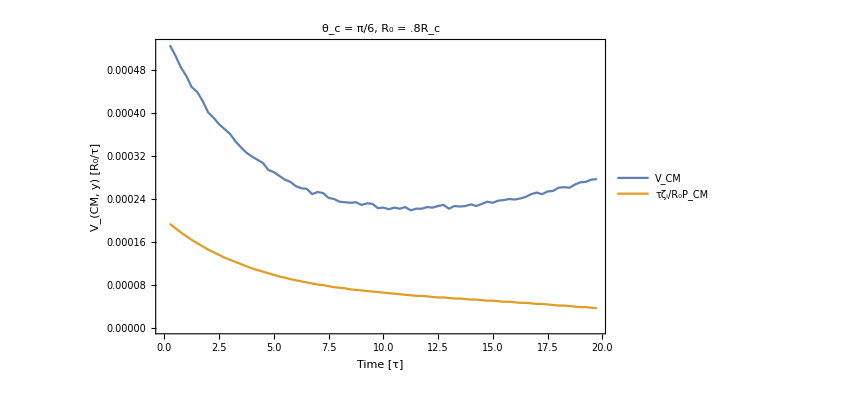

```mathematica
Vycm[simulName_]:=Transpose[{Normal[globalSols[[simulName,"Time",2;;]]],Normal[globalSols[[simulName,"Vycm",2;;]]]}];
VfromP[simulName_]:=Transpose[{Normal[globalSols[[simulName,"Time",2;;]]],Normal[globalSols[[simulName,"Pycm",2;;]]]}];

(*Normal[params[[simulName,"zi"]]]*Normal[params[[simulName,"tscale"]]]/(Normal[params[[simulName,"xi"]]]*Normal[params[[simulName,"R0"]]]))*)

(*Export[ToString[Row[{pathResults,simulNames[[1]]<>"_Vcm.svg"}]],*)
Show[ListLinePlot[{Vycm[simulNames[[2]]],VfromP[simulNames[[2]]]},
PlotLegends->Placed[{"V_CM","τζ_i/R_0P_CM"},Right],
LabelStyle->fontStyle,
PlotLabel->simulLegend[simulNames[[1]]],
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,Thickness->.002],
FrameLabel->{"Time [τ]","V_(CM, y) [R_0/τ]"},
LabelStyle->fontStyle,
TicksStyle->{fontStyle,fontStyle}],
ImageSize->imgSizePlot,
Background->White]
(*]*)
```

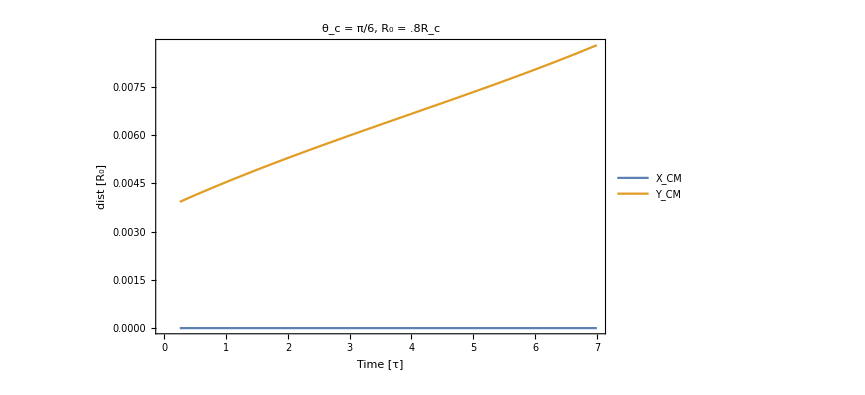

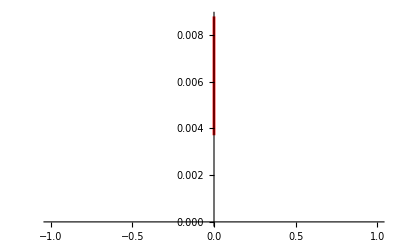

{<|Xcm→0.,Ycm→0.00371|>,<|Xcm→0.,Ycm→0.003926|>,<|Xcm→0.,Ycm→0.004137|>,<|Xcm→0.,Ycm→0.004341|>,<|Xcm→0.,Ycm→0.00454|>,<|Xcm→0.,Ycm→0.004734|>,<|Xcm→0.,Ycm→0.004924|>,<|Xcm→0.,Ycm→0.005109|>,<|Xcm→0.,Ycm→0.005291|>,<|Xcm→0.,Ycm→0.005469|>,<|Xcm→0.,Ycm→0.005645|>,<|Xcm→0.,Ycm→0.005818|>,<|Xcm→0.,Ycm→0.00599|>,<|Xcm→0.,Ycm→0.006159|>,<|Xcm→0.,Ycm→0.006328|>,<|Xcm→0.,Ycm→0.006496|>,<|Xcm→0.,Ycm→0.006664|>,<|Xcm→0.,Ycm→0.006832|>,<|Xcm→0.,Ycm→0.006999|>,<|Xcm→0.,Ycm→0.007168|>,<|Xcm→0.,Ycm→0.007339|>,<|Xcm→0.,Ycm→0.00751|>,<|Xcm→0.,Ycm→0.007684|>,<|Xcm→0.,Ycm→0.007861|>,<|Xcm→0.,Ycm→0.00804|>,<|Xcm→0.,Ycm→0.008223|>,<|Xcm→0.,Ycm→0.00841|>,<|Xcm→0.,Ycm→0.008601|>,<|Xcm→0.,Ycm→0.008798|>}

```mathematica
XcmTime[simulName_]:=Transpose[{Normal[globalSols[[simulName,"Time",2;;]]],Normal[globalSols[[simulName,"Xcm",2;;]]]}];
YcmTime[simulName_]:=Transpose[{Normal[globalSols[[simulName,"Time",2;;]]],Normal[globalSols[[simulName,"Ycm",2;;]]]}];



(*Export[ToString[Row[{pathResults,simulNames[[1]]<>"_Vcm.svg"}]],*)
Show[ListLinePlot[{XcmTime[simulNames[[1]]],YcmTime[simulNames[[1]]]},
PlotLegends->Placed[{"X_CM","Y_CM"},Right],
LabelStyle->fontStyle,
PlotLabel->simulLegend[simulNames[[1]]],
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,Thickness->.002],
FrameLabel->{"Time [τ]","dist [R_0]"},
LabelStyle->fontStyle,
TicksStyle->{fontStyle,fontStyle}],
ImageSize->imgSizePlot,
Background->White]
ListLinePlot[Normal[Transpose[globalSols[[simulName,{"Xcm","Ycm"},;;params[[simulName,"nFrames"]]]]]],PlotStyle->Directive[Red,Thickness[.005]]]
```

### Plot local fields

#### Static plots of timeframes

```mathematica
plotSimulFrame[simulName_,frame_,field_,plotLims_:{{-1.25,1.25},{-1.25,1.25}},plotOrigen_:{0,0}]:=Module[{m,mr,plotBack,plotFront(*,mesh*)},
m=Normal[localSols[[simulName,"mesh",frame]]];
mr=MeshRegion[m];
If[field=="velocity",
plotBack=DensityPlot[Sqrt[(Normal[localSols[[simulName,"vx",frame]]][x,y])^2+(Normal[localSols[[simulName,"vy",frame]]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"|v_α| (R_0/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"vx","vy"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="vorticity",
plotBack=DensityPlot[Normal[localSols[[simulName,"curlV",frame]]][x,y],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"∇×v_α (1/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"vx","vy"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="traction",
plotBack=DensityPlot[Sqrt[(Normal[localSols[[simulName,"px",frame]]][x,y])^2+(Normal[localSols[[simulName,"py",frame]]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"|p_α|"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"px","py"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
(*mesh=m["Wireframe"["MeshElementStyle"->Directive[FaceForm[(*col*)None],EdgeForm[Directive[Thickness[.003],Opacity[.15],Black(*Darker[col]*)]]]]];*)
Show[
ListPlot[{{-10,10}},AxesOrigin->plotOrigen],
plotBack,
plotFront,
(*mesh,*)
m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Thickness[.002],Black}]],
ListLinePlot[Normal[Transpose[globalSols[[simulName,{"Xcm","Ycm"},;;frame]]]],PlotStyle->Directive[Red,Thickness[.005]]],
PlotRange->plotLims,
AspectRatio->Automatic,
Background->White,
ImageSize->imgSizeSimul,
AxesStyle->Darker[Gray,.5],
LabelStyle->Join[fontStyle[[;;2]],{Darker[Gray,.5]}],
Epilog->{Inset[Framed[
Style[StringForm["A/A_0 = ``",NumberForm[Normal[globalSols[[simulName,"Area",frame]]]/Normal[globalSols[[simulName,"Area",1]]],3]],Join[fontStyle[[;;2]],{Darker[Gray,.5]}]],FrameStyle->Darker[Gray,.5]],{plotLims[[1,2]]-0.4,plotLims[[2,2]]-0.05}]},
PlotLabel->StringForm["`` of ``, t = ``",field,simulLegend[[simulName]],Normal[globalSols[[simulName,"Time",frame]]]]
]]
```

time_evol_1pi6_Lc50_08Rc

29

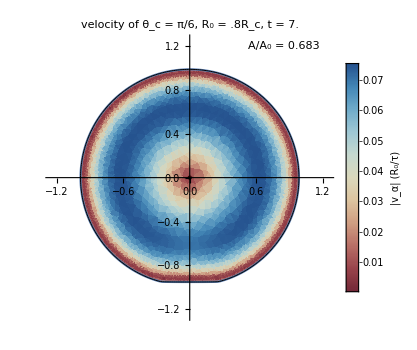
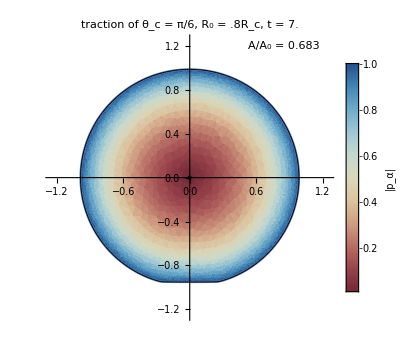
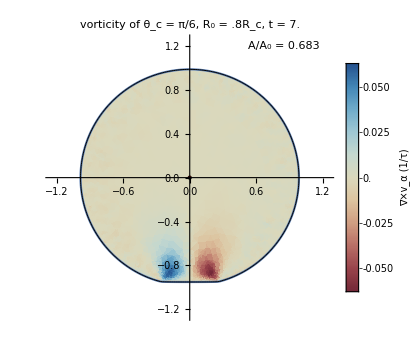

```mathematica
simulName=simulNames[[1]]
frame=params[[simulName,"nFrames"]]
Row[{plotSimulFrame[simulName,frame,"velocity"],plotSimulFrame[simulName,frame,"traction"],plotSimulFrame[simulName,frame,"vorticity"]}]
```

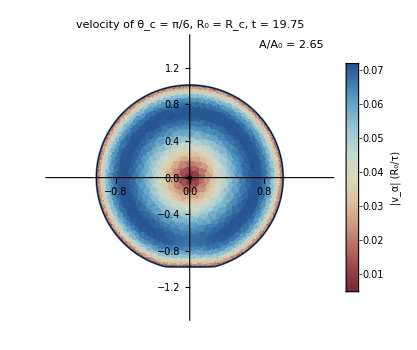
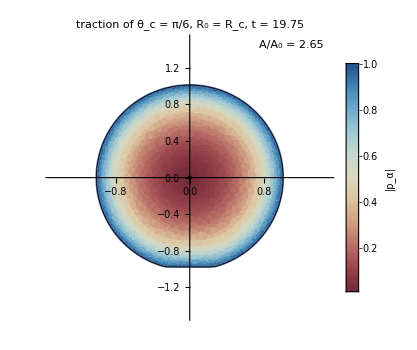
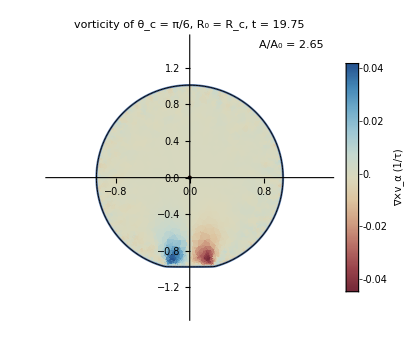

```mathematica
simulName=simulNames[[2]];
frame = 80;
plotLims={{-1.5,1.5},{-1.5,1.5}};
Row[{plotSimulFrame[simulName,frame,"velocity",plotLims],plotSimulFrame[simulName,frame,"traction",plotLims],plotSimulFrame[simulName,frame,"vorticity",plotLims]}]
```

#### Dynamic plots

```mathematica
(*Not fast and uses a lot of memory. It would need an optimization for extensive use.*)
plotSimul[simulName_,plotLims_:{{-1.25,1.25},{-1.25,1.25}},plotOrigen_:{0,0},scale_:1.5]:=Manipulate[
m=Normal[localSols[[simulName,"mesh",frame]]];
mr=MeshRegion[m];
If[field=="velocity",
plotBack=DensityPlot[Sqrt[(Normal[localSols[[simulName,"vx",frame]]][x,y])^2+(Normal[localSols[[simulName,"vy",frame]]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"|v_α| (R_0/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"vx","vy"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="vorticity",
plotBack=DensityPlot[Normal[localSols[[simulName,"curlV",frame]]][x,y],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"∇×v_α (1/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"vx","vy"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="traction",
plotBack=DensityPlot[Sqrt[(Normal[localSols[[simulName,"px",frame]]][x,y])^2+(Normal[localSols[[simulName,"py",frame]]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"|p_α|"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[Normal[localSols[[simulName,{"px","py"},frame]]][x,y],{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
(*mesh=m["Wireframe"["MeshElementStyle"->Directive[FaceForm[(*col*)None],EdgeForm[Directive[Thickness[.003],Opacity[.15],Black(*Darker[col]*)]]]]];*)
Show[
ListPlot[{{-10,10}},AxesOrigin->plotOrigen],
plotBack,
plotFront,
m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Thickness[.002],Black}]],
ListLinePlot[Normal[Transpose[globalSols[[simulName,{"Xcm","Ycm"},;;frame]]]],PlotStyle->Directive[Red,Thickness[.005]]],
PlotRange->plotLims,
AspectRatio->Automatic,
Background->White,
ImageSize->imgSizeSimul,
AxesStyle->Darker[Gray,.5],
LabelStyle->Join[fontStyle[[;;2]],{Darker[Gray,.5]}],
Epilog->{Inset[Framed[
Style[StringForm["A/A_0 = ``\ntime = ``",NumberForm[Normal[globalSols[[simulName,"Area",frame]]]/Normal[globalSols[[simulName,"Area",1]]],3],Normal[globalSols[[simulName,"Time",frame]]]],Join[fontStyle[[;;2]],{Darker[Gray,.5]}]],FrameStyle->Darker[Gray,.5]],{plotLims[[1,2]]-0.35,plotLims[[2,2]]-0.05}]},
PlotLabel->simulLegend[[simulName]]
],
Grid[{{Control[{{field,"velocity"},{"velocity","traction","vorticity"}}]},{Control[{frame,1,Normal[params[[simulName,"nFrames"]]],1}],SpanFromLeft,SpanFromLeft}}]]
```

```mathematica
plotSimul[simulNames[[1]]]
```

Part::pspec1: Part specification time_evol_1pi6_Lc50_08Rc is not applicable.

DensityPlot::idomdim: {x,y}∈mr does not have a valid dimension as a plotting domain.

Show::gcomb: Could not combine the graphics objects in Show[,VectorPlot[Normal[localSols⟦time_evol_1pi6_Lc50_08Rc,{vx,vy},FE`frame$$100⟧][x,y],{x,y}∈mr,VectorColorFunction→False,VectorStyle→{Thickness[0.001],Arrowheads[Tiny],Black},VectorPoints→20,RegionFillingStyle→None]].

Part::pspec1: Part specification time_evol_1pi6_Lc50_08Rc is not applicable.

ListLinePlot::lpn: Transpose[globalSols⟦time_evol_1pi6_Lc50_08Rc,{Xcm,Ycm},1;;8⟧] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 2 in fontStyle.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::pspec1: Part specification time_evol_1pi6_Lc50_08Rc is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in fontStyle.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Show::gcomb: Could not combine the graphics objects in Show[,«9»,«3»].

### Export the visualizations as .gif

```mathematica
gifSimul[simulName_,field_,plotLims_:{{-1.25,1.25},{-1.25,1.5}},plotOrigen_:{0,0}]:=Table[
m=Meshes[[simulName,frame]];
mr=MeshRegion[m];
If[field=="velocity",
plotBack=DensityPlot[Sqrt[(uxInts[[simulName,frame]][x,y])^2+(uyInts[[simulName,frame]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"|v_α| (R_0/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[{uxInts[[simulName,frame]][x,y],uyInts[[simulName,frame]][x,y]},{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="vorticity",
plotBack=DensityPlot[CurlUs[[simulName,frame]][x,y],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"∇×v_α (1/τ)"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[{uxInts[[simulName,frame]][x,y],uyInts[[simulName,frame]][x,y]},{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
If[field=="traction",
plotBack=DensityPlot[(ζi[simulName]*τ[simulName]/(ξ[simulName]*R0[simulName]))*Sqrt[(pxInts[[simulName,frame]][x,y])^2+(pyInts[[simulName,frame]][x,y])^2],{x,y}∈mr,PlotRange->All,
LabelStyle->fontStyle,
PlotLegends->{LegendLabel->"τζ_i/R_0|p_α|"},
ColorFunction->ColorData[palette](*(ColorData[palette][Rescale[#,{0.0,1.1}]]&)*)
(*ColorFunctionScaling->False*)];
plotFront=Show[Graphics[Point[{0,0}]],Quiet[VectorPlot[{pxInts[[simulName,frame]][x,y],pyInts[[simulName,frame]][x,y]},{x,y}∈mr,
VectorColorFunction->False,
VectorStyle->{Thickness[.001],Arrowheads[Tiny],Black},
VectorPoints->20,
RegionFillingStyle->None]]];
];
(*mesh=m["Wireframe"["MeshElementStyle"->Directive[FaceForm[(*col*)None],EdgeForm[Directive[Thickness[.003],Opacity[.15],Black(*Darker[col]*)]]]]];*)
Show[
ListPlot[{{-10,10}},AxesOrigin->plotOrigen],
plotBack,
plotFront,
(*mesh,*)
m["Wireframe"["MeshElement"->"BoundaryElements","MeshElementStyle"->{Thickness[.002],Black}]],
ListLinePlot[XYcms[[simulName,;;frame]],PlotStyle->Directive[Red,Thickness[.005]]],
PlotRange->plotLims,
AspectRatio->Automatic,
Background->White,
ImageSize->imgSizeGif,
AxesStyle->Darker[Gray,.5],
LabelStyle->Join[fontStyle[[;;2]],{Darker[Gray,.5]}],
Epilog->{Inset[Framed[
Style[StringForm["A/A_0 = ``\ntime = ``",NumberForm[area[[simulName,frame]]/area[[simulName,1]],3],time[[simulName,frame]]],Join[fontStyle[[;;2]],{Darker[Gray,.5]}]],FrameStyle->Darker[Gray,.5]],{plotLims[[1,2]]-0.35,plotLims[[2,2]]-0.05}]},
PlotLabel->field<>" of "<>simulLegend[[simulName]]
],{frame,1,nFrames[[simulName]],1}]
```

```mathematica
simulName=simulNames[[1]];
field="velocity";
Export[ToString[Row[{pathResults,simulName<>"_"<>field<>".gif"}]],gifSimul[simulName,field],ImageResolution->120,AnimationRepetitions->Infinity,"DisplayDurations"->.02*gsplit]
```

results/MDA-MB-231_1pi2_Rc_velocity.gif

```mathematica
simulName=simulNames[[2]];
field="velocity";
plotLims={{-2,2},{-.5,6.}};
Export[ToString[Row[{pathResults,simulName<>"_"<>field<>".gif"}]],gifSimul[simulName,field,plotLims],ImageResolution->240,AnimationRepetitions->Infinity,"DisplayDurations"->.02*gsplit]
```

results/A431_1pi2_doubleRc_velocity.gif

## In Development

### Compute and visualize the curvature

```mathematica
matA[points_]:=Map[Join[#,{1}]&,points];
matB[points_]:=Map[{#.#,#[[2]],1}&,points];
matC[points_]:=Map[{#.#,#[[1]],1}&,points];
matD[points_]:=Map[Join[{#.#},#]&,points];
coefA[points_]:=Det[matA[points]];
coefB[points_]:=-Det[matB[points]];
coefC[points_]:=Det[matC[points]];
coefD[points_]:=-Det[matD[points]];
r3[points_]:=Sqrt[(coefB[points]^2+coefC[points]^2-4 coefA[points] coefD[points])/(10^-8+4 coefA[points]^2)];

signκ[points_]:=-Sign[(Normalize[points[[3]]-points[[2]]]-Normalize[points[[2]]-points[[1]]]).points[[2]]];

BoundaryCoordinatesSupport=Map[Join[{#[[-1]]},#,{#[[1]]}]&,SortedBCs[[1]]];
κBoundary=ParallelMap[Table[Join[#[[i+1]],{signκ[Take[#,{i,i+2}]]/(10^-8+r3[Take[#,{i,i+2}]])}],{i,1,Length[#]-2}]&,BoundaryCoordinatesSupport];
```

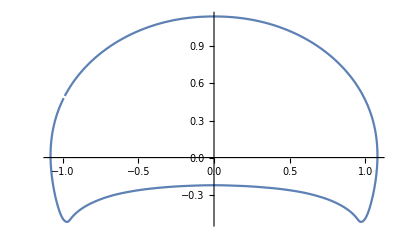

-Graphics3D-

```mathematica
ListLinePlot[SortedBCs[[1]][[30]]]
ListPointPlot3D[κBoundary[[30]]]
```

### Compute and visualize the phase field

```mathematica
(*S is the spreading parameter, ηV, and S=0 gives us the critical radius for the wetting transition of the circle*)
S[R_,ζ_,ζi_,Lc_]:=ζ*R/2-2*ζi*Lc*Lc+(ζ*Lc+ζi*Lc*R)*(BesselI[0,R/Lc]/BesselI[1,R/Lc])-(ζ*R/2)*(BesselI[0,R/Lc]/BesselI[1,R/Lc])*(BesselI[0,R/Lc]/BesselI[1,R/Lc])

simulName =simulNames[[2]];
Raprox=.5*(3*Lc[[simulName]]-ζ[[simulName]]/ζi[[simulName]]);
solR = FindRoot[S[R,ζ[[simulName]],ζi[[simulName]],Lc[[simulName]]],{R,Raprox}][[1,2]];
Print["Real Rc=",solR,", aprox Rc=",Raprox];

(*Adimesnionalized version of S*)
(*La=Abs[ζ]/ζi;*)
(*a=La/Lc;*)
a[simulName_]:=Abs[ζ[[simulName]]]/(ζi[[simulName]]*Lc[[simulName]]);
xaprox =(3+Abs[ζ[[simulName]]]/(ζi[[simulName]]*Lc[[simulName]]))/2;

adimS[x_,a_]:=-(a*x/2+2)+(x-a)*(BesselI[0,x]/BesselI[1,x])+(a*x/2)*(BesselI[0,x]/BesselI[1,x])*(BesselI[0,x]/BesselI[1,x])

x0= FindRoot[adimS[x,Abs[ζ[[simulName]]]/(ζi[[simulName]]*Lc[[simulName]])],{x,xaprox}][[1,2]];
Print["Real Rc=",x0*Lc[[simulName]],", aprox Rc=",xaprox*Lc[[simulName]]];
```

Real Rc=12.9439, aprox Rc=29.1667

Real Rc=12.9439, aprox Rc=29.1667

```mathematica
(*Adimesnionalized version of S*)
(*La=Abs[ζ]/ζi;*)
(*a=La/Lc;*)

La=200;
c=4; (*c=R0/Lc*)
areaCst=<|"1pi6"->3.129442,"1pi3"->3.050529,"2pi3"->2.525833,"3pi3"->1.565346,"4pi3"->0.595408|>
R0[R_,cut_]:=Sqrt[Pi/areaCst[[cut]]]*R
a[R0_]:=c*La/R0;
x[cut_]:=Sqrt[areaCst[[cut]]/Pi]*c;

R0cLin[cut_]:=La/(2*(Sqrt[areaCst[[cut]]/Pi]-3/(2*c)));

adimS[R0_,cut_]:=-(a[R0]*x[cut]/2+2)+(x[cut]-a[R0])*(BesselI[0,x[cut]]/BesselI[1,x[cut]])+(a[R0]*x[cut]/2)*(BesselI[0,x[cut]]/BesselI[1,x[cut]])*(BesselI[0,x[cut]]/BesselI[1,x[cut]])

R0c= <|#->FindRoot[adimS[R0,#],{R0,R0cLin[#]}][[1,2]]&/@Keys[areaCst]|>
Print["cut ",#,", exact R0 = ",R0c[#],", linear R0 = ",R0cLin[#]]&/@Keys[areaCst];
```

<|1pi6→3.12944,1pi3→3.05053,2pi3→2.52583,3pi3→1.56535,4pi3→0.595408|>

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

<|1pi6→145.007,1pi3→147.445,2pi3→166.806,3pi3→227.601,4pi3→413.227|>

cut 1pi6, exact R0 = 145.007, linear R0 = 160.497

cut 1pi3, exact R0 = 147.445, linear R0 = 163.827

cut 2pi3, exact R0 = 166.806, linear R0 = 191.696

cut 3pi3, exact R0 = 227.601, linear R0 = 302.225

cut 4pi3, exact R0 = 413.227, linear R0 = 1657.17

```mathematica
shapeFactor[simulName_]:=Sqrt[2*Pi/(2*Pi-cut[[simulName]]+Sin[cut[[simulName]]])]
Revo[simulName_]:=Transpose[{ConstantArray[a[simulName ],nFrames[[simulName]]],Sqrt[area[simulName]/(Pi*shapeFactor[simulName])]*R0[[simulName]]/(Lc[[simulName]])}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

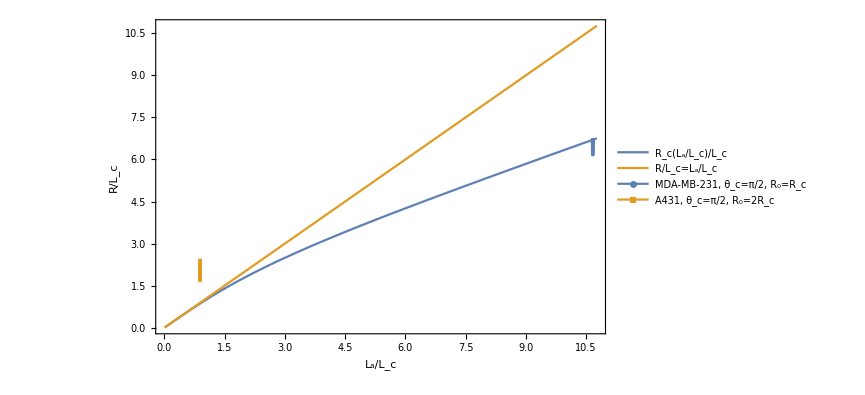

```mathematica
amax=a[simulNames[[1]]]+0.1; (*maximum a, little bit higher that Ricard's a*)
aRange=Subdivide[amax,1000][[2;;]];

xvsa={#,FindRoot[adimS[x,#],{x,(3+#)/2}][[1,2]]}&/@aRange;(*x=Rc/Lc as a function of a*)
xeqa ={#,#}&/@aRange; (*R/Lc=La/Lc condition*)
xaproxa={#,(3+#)/2}&/@aRange; 
Show[ListLinePlot[{xvsa,xeqa},
PlotLegends->Placed[{"R_c(L_a/L_c)/L_c","R/L_c=L_a/L_c"},Right],
LabelStyle->fontStyle,
(*PlotLabel->"V_(CM, y)(t)",*)
Frame->{{True,False},{True,False}},
FrameStyle->Directive[Black,Thickness->.002],
FrameLabel->{"L_a/L_c","R/L_c"},
LabelStyle->fontStyle,
TicksStyle->{fontStyle,fontStyle}],
ListLinePlot[Revo[#]&/@simulNames,
LabelStyle->fontStyle,
PlotLegends->Placed[simulLegend[#]&/@simulNames,Right],
PlotMarkers->{Automatic,Tiny}
],
ImageSize->imgSizePlot,
Background->White]
```